```mathematica
(* AbelianGroup[{2,2,3}]//GroupOrder *)
```

```mathematica
AbelianGroup[{2,2,3}]
```

AbelianGroup[{2,2,3}]

```mathematica
GroupStabilizerChain[AbelianGroup[{2,2,3}]]
```

{{}→PermutationGroup[{Cycles[{{1,2}}],Cycles[{{3,4}}],Cycles[{{5,6,7}}]}],{1}→PermutationGroup[{Cycles[{{3,4}}],Cycles[{{5,6,7}}]}],{1,3}→PermutationGroup[{Cycles[{{5,6,7}}]}],{1,3,5}→PermutationGroup[{}]}

```mathematica
PermutationCycleIndexPolynomial[AbelianGroup[{2,2,3}],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7]}]
```

PermutationCycleIndexPolynomial[AbelianGroup[{2,2,3}],{x_1,x_2,x_3,x_4,x_5,x_6,x_7}]

```mathematica
GroupElementToWord[AbelianGroup[{2,2,3}],RawBoxes[RowBox[{RowBox[{RowBox[{"Cyles","[",RowBox[{RowBox[{"{",RowBox[{"1",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"5",",","7",",","6"}],"}"}]}]}],"}"}],"]"}]]]
```

GroupElementToWord::perm: Cyles[{1,2},{5,7,6}}] is not a valid permutation.

GroupElementToWord[AbelianGroup[{2,2,3}],Cyles[{1,2},{5,7,6}}]]

```mathematica
PermutationSupport[AbelianGroup[{2,2,3}]]
```

{1,2,3,4,5,6,7}

```mathematica
GroupElementQ[AbelianGroup[{2,2,3}],2]
```

GroupElementQ::perm: 2 is not a valid permutation.

GroupElementQ[AbelianGroup[{2,2,3}],2]

```mathematica
RandomPermutation[AbelianGroup[{2,2,3}]]
```

Cycles[{{1,2},{5,7,6}}]

```mathematica
GroupOrbits[AbelianGroup[{2,2,3}]]
```

{{1,2},{3,4},{5,6,7}}

```mathematica
GroupMultiplicationTable[AbelianGroup[{2,2,3}]]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{2,3,1,5,6,4,8,9,7,11,12,10},{3,1,2,6,4,5,9,7,8,12,10,11},{4,5,6,1,2,3,10,11,12,7,8,9},{5,6,4,2,3,1,11,12,10,8,9,7},{6,4,5,3,1,2,12,10,11,9,7,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,9,7,11,12,10,2,3,1,5,6,4},{9,7,8,12,10,11,3,1,2,6,4,5},{10,11,12,7,8,9,4,5,6,1,2,3},{11,12,10,8,9,7,5,6,4,2,3,1},{12,10,11,9,7,8,6,4,5,3,1,2}}

```mathematica
GroupGenerators[AbelianGroup[{2,2,3}]]
```

{Cycles[{{1,2}}],Cycles[{{3,4}}],Cycles[{{5,6,7}}]}

```mathematica
CayleyGraph[AbelianGroup[{2,2,3}]]
```

-Graphics-

```mathematica
GroupElements[AbelianGroup[{2,2,3}]]
```

{Cycles[{}],Cycles[{{5,6,7}}],Cycles[{{5,7,6}}],Cycles[{{3,4}}],Cycles[{{3,4},{5,6,7}}],Cycles[{{3,4},{5,7,6}}],Cycles[{{1,2}}],Cycles[{{1,2},{5,6,7}}],Cycles[{{1,2},{5,7,6}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,2},{3,4},{5,6,7}}],Cycles[{{1,2},{3,4},{5,7,6}}]}

```mathematica
GroupOrder[AbelianGroup[{2,2,3}]]
```

12

```mathematica
LinearProgramming[{1,1},{{1,2}},{3}]
```

{0,3/2}

```mathematica
LinearProgramming[{1,1},{{1,2}},{{3,0}}]
```

{0,3/2}

```mathematica
Plot3D[x+y,{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
4/3 π r^3
```

(4 π r^3)/3

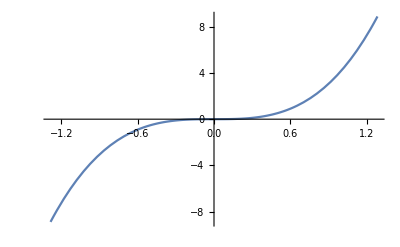

```mathematica
Plot[(4 π r^3)/3,{r,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
(4 π 1^3)/3
```

(4 π)/3

```mathematica
N@((4 π)/3)
```

4.18879

```mathematica
(4 π)/3==∫_0^((4π)/3) 1ⅆr
```

True

```mathematica
a==∫_0^a ⅆr
```

True

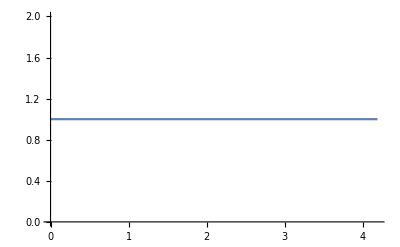

```mathematica
Plot[1,{x,0,(4π)/3}]
```

```mathematica
Volume[Sphere[]]
```

Undefined

```mathematica
Graphics3D[Point[SpherePoints[200]]]
```

-Graphics3D-



```mathematica
Plot[x x,{x,-2,2}]
```

```mathematica
SphericalPlot3D[1,{θ,0,2π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
2∫_1^0 √(1-x^2)ⅆx
```

-π/2

```mathematica
2∫_r^0 √(r-x^2)ⅆx
```

ConditionalExpression[-r (√(-(-1+r) r)+ArcTan[r/(√(-(-1+r) r))]),2 Re[r]≥2+r^2+Conjugate[r]^2&&(√(1/Re[r])∉ℝ||(r Conjugate[r])/Re[r]≥2||Re[√(1/Re[r])]≥√2||Re[√(1/Re[r])]≤0)]

```mathematica
FullSimplify[2∫_r^0 √(r-x^2)ⅆx,r∈Reals]
```

$Aborted

```mathematica
FullSimplify[2∫_r^0 √(r-x^2)ⅆx,r∈]
```

Undefined

```mathematica
2∫_-r^r √(r-x^2)ⅆx
```

$Aborted

```mathematica
2∫_0^r √(r-x^2)ⅆx
```

ConditionalExpression[r (√(-(-1+r) r)+ArcTan[r/(√(-(-1+r) r))]),((r Conjugate[r])/Re[r]≥0&&(0<Re[√r]<1||(Re[√r]≤1&&r≤0)))||((Re[√Re[r]]≤1/(√2)||√Re[r]∉ℝ)&&((Re[√r]≤1&&(Re[r]<0||0<Re[√r]<1||r∉ℝ))||√r∉ℝ))]

```mathematica
∫_-1^1 √(1-x^2)ⅆx
```

π/2

```mathematica
2∫_-1^1 √(1-x^2)ⅆx
```

π

```mathematica
(2∫_-1^1 √(1-x^2)ⅆx)r^2
```

π r^2

```mathematica
∫_-1^1 ((2∫_-1^1 √(1-x^2)ⅆx)r^2)ⅆx
```

2 π r^2